## Definitions

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
readStanDataset[filename_]:=Module[{rawD},
	rawD=Import[filename]//Select[NumberQ[#[[1]]]||StringTake[#[[1]],1]!="#"&];
	Dataset[AssociationThread[rawD[[1]],#]&/@Rest[rawD]]
]
```

```mathematica
paramInEllipsoidQ[θ_, θStar_, cov_] := Module[{x, invMat},
	x = θ - θStar;
	invMat = Inverse[cov];
	x.invMat.x < 1
]
```

```mathematica
(*This is from Reichl et al 2020. Adapted using MatrixPower[#, 1/2] to give correct results.*)
getEllDraw[θStar_, cov_] := Module[
	{k, rs, pt, λs, λh, eVals, eVecs},
	k = Length@cov;
	rs = RandomVariate[UniformDistribution[]];
	pt = RandomVariate[NormalDistribution[], k];
	λs = Total[pt^2];
	λh = rs^(1/k)/√λs;
	eVals = Eigenvalues[MatrixPower[cov, 1/2]];
	eVecs = Eigenvectors[MatrixPower[cov, 1/2]];
	(λh pt eVals).eVecs + θStar
]
```

```mathematica
(*This is from Reichl et al. 2020*)
getEllipsoidVolume[mat_] := Module[
	{k = Length@mat, v, e, i},
	v = Table[0, k+1];
	e = Eigenvalues@mat;
	v[[1]] = Log[1];
	v[[2]] = Log[2];
	For[i=3, i<=k+1, i++, v[[i]] = Log[(2Pi)/(i - 1)] + v[[i-2]]];
	v[[k+1]] + Total[Log@Sqrt[e]]
]
```

```mathematica
(*The following is from Reichl 2020 Appendix A.3*)
getAlpha[posteriorDraws_, unnormalisedLoglValues_, θStar_, d_]:=Module[
	{lP, l, ρ, lpHigh, logLValues, lpLow, αLow=0.01, αHigh=100.0, α, αMax, αMin, c, δA, zip},
	l = Length@posteriorDraws;
	ρ = Median[unnormalisedLoglValues];
	lP = 0.49l;
	αMax = αHigh;
	αMin = αLow;
	δA = αHigh - αLow;
	c = 0;
	While[δA > 0.1,
		δA = αHigh - αLow;
		{lpLow, lpHigh} = Table[
			zip = Transpose[{posteriorDraws, unnormalisedLoglValues}];
			Length[Select[zip, paramInEllipsoidQ[#[[1]], θStar, α d] && #[[2]] > ρ &]],
			{α, {αLow, αHigh}}
		];
		If[lpHigh > lP,
			If[c==0, αMax = Max[αHigh, αMax], If[αHigh<αMax, αMax=αHigh]];
			αHigh=(αLow+αHigh)/2;
			c=1;,
			If[c==1, αHigh=Min[αHigh+10,αMax], αHigh=αHigh+100]
		];
		If[lpLow<lP,
			If[αLow>αMin,αMin==αLow];
			αLow=(αLow+αHigh)/2;,
			αLow=Max[(1+αLow)/2,αMin];
		]
	];
	αHigh
]
```

```mathematica
logMarginalLikelihood[posteriorDraws_,loglValues_,logLfunc_] := Module[
	{ρ, d, maxLogl, maxIndex, θStar,α,ellDraws,piHat,logIntegrationVolume,logκ},
	ρ=Median@loglValues;
	d=Covariance@posteriorDraws;
	maxLogl=Max@loglValues;
	maxIndex=Ordering[loglValues,-1]//First;
	θStar=posteriorDraws[[maxIndex]];
	α=getAlpha[posteriorDraws,loglValues,θStar,d];
	Print["Estimating α as ", α];
	ellDraws=Table[getEllDraw[θStar,α d],1000];
	piHat=N[Length@Select[ellDraws,logLfunc[#]>ρ&]/Length@ellDraws];
	Print["Estimating piHat as ", piHat];
	logIntegrationVolume=getEllipsoidVolume[α d]+Log[piHat];
	logκ=Log[Mean[
		MapThread[
			If[paramInEllipsoidQ[#1,θStar,α d]&&#2>ρ,1/Exp[#2-ρ],0]&,
			{posteriorDraws,loglValues}
		]
	]] - ρ;
	logIntegrationVolume - logκ
]
```

## Tests

### Ellipsoid Sampling tests

Let’s define an arbitrary two-dimensional covariance matrix, and a mid-point of (0.5, 0.5):

```mathematica
θStar={0.5,0.5};cov={{0.1,0.08},{0.08,0.2}};
MatrixForm[cov]
```

(0.1 | 0.08
0.08 | 0.2)

Sampling within and coloring using the paramInEllipsoidQ function:

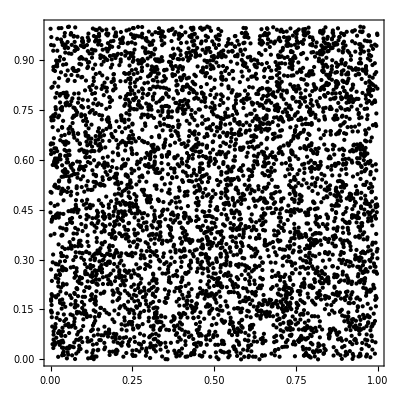

```mathematica
randomPoints=RandomVariate[UniformDistribution[10000]]//Partition[#,2]&;
colors=Table[If[paramInEllipsoidQ[p,θStar,cov],Red,Blue],{p,randomPoints}];
Graphics[
Point[randomPoints,VertexColors->colors],AspectRatio->1,ImagePadding->20,Frame->True]
```

Now performing random sampling using getEllDraw and overlaying with the above sampled points:

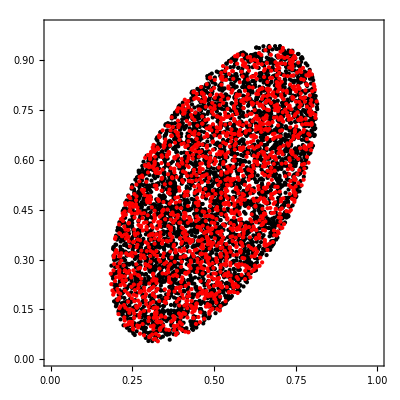

```mathematica
randomPoints2=Table[getEllDraw[θStar,cov],4000];
Graphics[
{
Black,Point[randomPoints2],
Red,Point[Select[randomPoints,paramInEllipsoidQ[#,θStar,cov]&]]
},
AspectRatio->1,ImagePadding->20,Frame->True,PlotRange->{{0,1},{0,1}}
]
```

Looks right, but I had to tweak the original function from Reichl. et al to take the “Square root” of the matrix first, see above.

### Ellipsoid Volume test

```mathematica
dimensions={1,2,3,4};
radii={1,2,3,4};
TableForm[
Table[
{
d,
Exp[getEllipsoidVolume[IdentityMatrix[d]]],
Exp[getEllipsoidVolume[DiagonalMatrix[radii[[;;d]]]]],
Exp[getEllipsoidVolume[2^2 IdentityMatrix[d]]]
},
{d,dimensions}
],
TableHeadings->{None, {"Dimension","Volume Unit Sphere", "Volume Ellipsoid","Volume twice Unit Sphere"}}
]
```

Dimension | Volume Unit Sphere | Volume Ellipsoid | Volume twice Unit Sphere
1 | 2 | 2 | 4
2 | π | √2 π | 4 π
3 | (4 π)/3 | 4 √(2/3) π | (32 π)/3
4 | π^2/2 | √6 π^2 | 8 π^2

This looks right. It seems the input matrix must be in the form of a covariance matrix, where the radii are considered squared

### Simple two-dimensional case study

We consider a two-dimensional parameter space with flat priors from 0 to 1:

```mathematica
priorDist=ProductDistribution[
UniformDistribution[],
UniformDistribution[]
];
```

And a posterior as a Normal distribution centered in the middle:

```mathematica
posteriorDist=MultinormalDistribution[{0.5,0.5},{{0.002,0.002},{0.002,0.006}}];
```

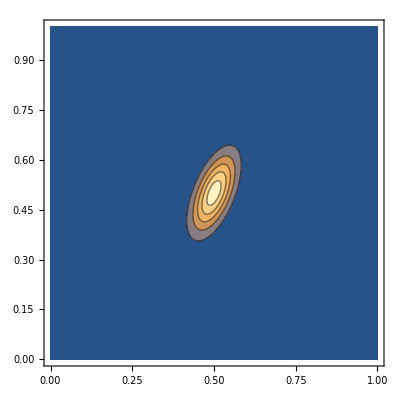

```mathematica
ContourPlot[PDF[posteriorDist,{x,y}],{x,0,1},{y,0,1},PlotRange->All]
```

We define a fake unnormalised likelihood function with a fake normalisation constant of 10^-6:

```mathematica
logLfunc[θ_]:=Log[10^-6]+LogLikelihood[posteriorDist,{θ}]
```

#### Naive computation using prior draws

We can first use the naive marginal likelihood estimator using prior draws:

```mathematica
priorDraws=RandomVariate[priorDist,10000];
loglValues=logLfunc/@priorDraws;
```

with a maximum of

```mathematica
scale=Max[loglValues]
```

-9.78622

which we use to scale and compute the log-evidence as mean of the loglValues on the prior draws:

```mathematica
Log[Mean[Exp[loglValues-scale]]]+scale
```

-13.7577

which is pretty close to our theoretical value of

```mathematica
N@Log[10^-6]
```

-13.8155

#### Reichl 2020 Method

We first create fake draws from the posterior, mimicking an MCMC outcome:

```mathematica
posteriorDraws=RandomVariate[posteriorDist,2000];
```

and compute the unnormalised likelihood values for it:

```mathematica
loglValues=logLfunc/@posteriorDraws;
```

and set up the necessary quantities:

```mathematica
ρ=Median@loglValues
d=Covariance@posteriorDraws
maxLogl=Max@loglValues
maxIndex=Ordering[loglValues,-1]//First
θStar=posteriorDraws[[maxIndex]]
```

-10.4634

{{0.00199751,0.00186824},{0.00186824,0.00581537}}

-9.78644

1777

{0.498473,0.500473}

We compute alpha:

```mathematica
α=getAlpha[posteriorDraws,loglValues,θStar,d]
```

1.45887

Drawing points from the ellipsoid

```mathematica
ellDraws=Table[getEllDraw[θStar,α d],1000];
```

Estimating how many of them are in the integration volume:

```mathematica
piHat=Length@Select[ellDraws,logLfunc[#]>ρ&]/Length@ellDraws
```

919/1000

```mathematica
logIntegrationVolume=getEllipsoidVolume[α d]+Log[piHat]
```

-4.4223

And estimating κ according to equation 2.1

```mathematica
logκ=Log[Mean[
MapThread[
If[paramInEllipsoidQ[#1,θStar,α d]&&#2>ρ,1/Exp[#2-ρ],0]&,
{posteriorDraws,loglValues}
]
]]-ρ
```

9.41555

And get as final result

```mathematica
logIntegrationVolume-logκ
```

-13.8379

which is very close to

```mathematica
N@Log[10^-6]
```

-13.8155

#### Reichl 2020 Method as one function

```mathematica
logMarginalLikelihood[posteriorDraws,loglValues]
```

Estimating α as 1.45887

Estimating piHat as 0.918

-13.8389

### A five-dimensional case study

We consider a five-dimensional parameter space with flat priors from 0 to 1:

```mathematica
priorDist=ProductDistribution[Sequence@@Table[UniformDistribution[],5]]
```

ProductDistribution[UniformDistribution[{0,1}],UniformDistribution[{0,1}],UniformDistribution[{0,1}],UniformDistribution[{0,1}],UniformDistribution[{0,1}]]

And a posterior as a Normal distribution centered in the middle:

```mathematica
posteriorDist=MultinormalDistribution[{0.5,0.5,0.5,0.5,0.5},DiagonalMatrix[{0.002,0.002,0.002,0.002,0.002}]]
```

MultinormalDistribution[{0.5,0.5,0.5,0.5,0.5},{{0.002,0.,0.,0.,0.},{0.,0.002,0.,0.,0.},{0.,0.,0.002,0.,0.},{0.,0.,0.,0.002,0.},{0.,0.,0.,0.,0.002}}]

We define a fake unnormalised likelihood function with a fake normalisation constant of 10^-6:

```mathematica
logLfunc[θ_]:=Log[10^-6]+LogLikelihood[posteriorDist,{θ}]
```

#### Naive Method

```mathematica
priorDraws=RandomVariate[priorDist,10000];
loglValues=logLfunc/@priorDraws;
```

with a maximum of

```mathematica
scale=Max[loglValues]
```

-6.51692

which we use to scale and compute the log-evidence as mean of the loglValues on the prior draws:

```mathematica
Log[Mean[Exp[loglValues-scale]]]+scale
```

-14.8227

which is far below our theoretical expectation

```mathematica
N@Log[10^-6]
```

-13.8155

#### Reichl method

```mathematica
posteriorDraws=RandomVariate[posteriorDist,2000];
```

and compute the unnormalised likelihood values for it:

```mathematica
loglValues=logLfunc/@posteriorDraws;
```

```mathematica
logMarginalLikelihood[posteriorDraws,loglValues]
```

Estimating α as 4.9115

Estimating piHat as 0.751

-13.8088

Perfect!

## Sibling model

```mathematica
stanData=readStanDataset["model_siblings_output.csv"];
```

```mathematica
stanData
```

Dataset[<>]

```mathematica
columns=stanData[1,Keys]//Normal
```

{lp__,accept_stat__,stepsize__,treedepth__,n_leapfrog__,divergent__,energy__,birth_date_mother,mother_age_hochdorf,mother_age_asperg,age_hochdorf,age_asperg,burial_date_hochdorf,burial_date_asperg}

```mathematica
variableNames=Drop[columns,7]
```

{birth_date_mother,mother_age_hochdorf,mother_age_asperg,age_hochdorf,age_asperg,burial_date_hochdorf,burial_date_asperg}

```mathematica
priorDists={
UniformDistribution[{-600,-500}],
NormalDistribution[30,6],
NormalDistribution[30,6],
NormalDistribution[45,6],
NormalDistribution[30,6],
NormalDistribution[-530,6],
NormalDistribution[-490,6]
};
```

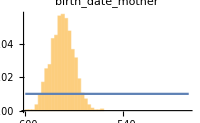
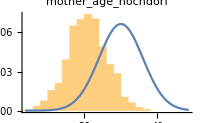
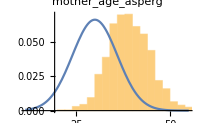
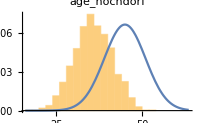
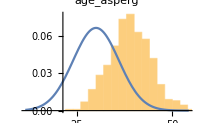
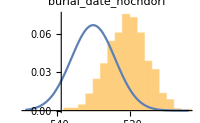
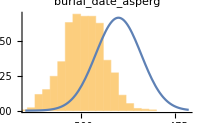

```mathematica
Module[
{d,pd,left,right},
Row[
Table[
v=variableNames[[i]];
d=stanData[All,v];
pd=priorDists[[i]];
left=Min[Quantile[d,0.001],Quantile[pd,0.001]];
right=Max[Quantile[d,0.999],Quantile[pd,0.999]];
Show[
Histogram[d,Automatic,"PDF",PlotLabel->v,ImageSize->200,Axes->{True,False}],
Plot[PDF[pd,x],{x,left,right}],
PlotRangeClipping->True,PlotRange->{{left, right},All}
],
{i,Length@variableNames}
],
Spacer[20]
]
]
```

```mathematica
TableForm[Table[Quantile[stanData[All,v],#]&/@{0.05,0.5,0.95},{v,variableNames}],TableHeadings->{variableNames,{"5-Percentile","Median","95-Percentile"}}]
```

| 5-Percentile | Median | 95-Percentile
birth_date_mother | -588.656 | -577.266 | -566.133
mother_age_hochdorf | 11.2697 | 20.7575 | 29.6282
mother_age_asperg | 30.7118 | 38.774 | 48.4151
age_hochdorf | 26.6839 | 35.6367 | 44.8355
age_asperg | 29.9564 | 38.981 | 47.6571
burial_date_hochdorf | -529.527 | -520.727 | -512.087
burial_date_asperg | -508.492 | -499.129 | -490.57

```mathematica
paramNames=variableNames[[;;-3]]
```

{birth_date_mother,mother_age_hochdorf,mother_age_asperg,age_hochdorf,age_asperg}

```mathematica
combinedPrior=ProductDistribution@@(priorDists[[;;5]])
```

ProductDistribution[UniformDistribution[{-600,-500}],NormalDistribution[30,6],NormalDistribution[30,6],NormalDistribution[45,6],NormalDistribution[30,6]]

```mathematica
logLSiblings[paramVector_]:=Module[{mothersBirthDate,birthAgeH,birthAgeA,ageH,ageA,burialDateH,burialDateA},
{mothersBirthDate,birthAgeH,birthAgeA,ageH,ageA}=paramVector;
burialDateH=mothersBirthDate+birthAgeH+ageH;
burialDateA=mothersBirthDate+birthAgeA+ageA;
LogLikelihood[combinedPrior,{paramVector}]+LogLikelihood[NormalDistribution[-530.,6],{burialDateH}]+
LogLikelihood[NormalDistribution[-490.,6],{burialDateA}]
]
```

```mathematica
posteriorDraws=stanData[All,paramNames/*Values]//Normal;
```

```mathematica
posteriorLogLvalues=logLSiblings/@posteriorDraws;
```

```mathematica
logMarginalLikelihood[posteriorDraws,posteriorLogLvalues,logLSiblings]
```

Estimating α as 4.76855

Estimating piHat as 0.754

-15.2852

## Avuncular model

```mathematica
stanData=readStanDataset["model_avuncular_output.csv"];
```

```mathematica
stanData
```

Dataset[<>]

```mathematica
columns=stanData[1,Keys]//Normal
```

{lp__,accept_stat__,stepsize__,treedepth__,n_leapfrog__,divergent__,energy__,birth_date_mother,mother_age_hochdorf,mother_age_sister,sister_age_asperg,age_hochdorf,age_asperg,burial_date_hochdorf,burial_date_asperg}

```mathematica
variableNames=Drop[columns,7]
```

{birth_date_mother,mother_age_hochdorf,mother_age_sister,sister_age_asperg,age_hochdorf,age_asperg,burial_date_hochdorf,burial_date_asperg}

```mathematica
priorDists={
UniformDistribution[{-650,-550}],
NormalDistribution[30,6],
NormalDistribution[30,6],
NormalDistribution[30,6],
NormalDistribution[45,6],
NormalDistribution[30,6],
NormalDistribution[-530,6],
NormalDistribution[-490,6]
};
```

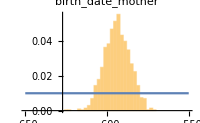
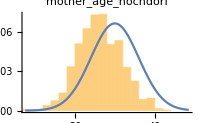
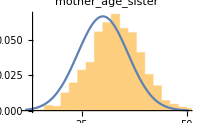
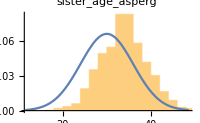
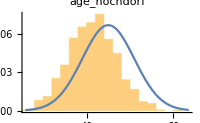
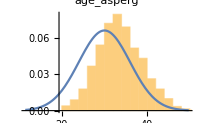
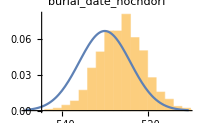
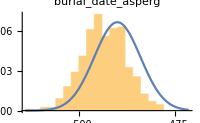

```mathematica
Module[
{d,pd,left,right},
Row[
Table[
v=variableNames[[i]];
d=stanData[All,v];
pd=priorDists[[i]];
left=Min[Quantile[d,0.001],Quantile[pd,0.001]];
right=Max[Quantile[d,0.999],Quantile[pd,0.999]];
Show[
Histogram[d,Automatic,"PDF",PlotLabel->v,ImageSize->200,Axes->{True,False}],
Plot[PDF[pd,x],{x,left,right}],
PlotRangeClipping->True,PlotRange->{{left, right},All}
],
{i,Length@variableNames}
],
Spacer[20]
]
]
```

```mathematica
TableForm[Table[Quantile[stanData[All,v],#]&/@{0.05,0.5,0.95},{v,variableNames}],TableHeadings->{variableNames,{"5-Percentile","Median","95-Percentile"}}]
```

| 5-Percentile | Median | 95-Percentile
birth_date_mother | -606.288 | -593.939 | -581.223
mother_age_hochdorf | 17.7305 | 26.0627 | 35.3283
mother_age_sister | 22.9026 | 32.8823 | 42.6275
sister_age_asperg | 25.3535 | 33.8852 | 42.4577
age_hochdorf | 32.3665 | 41.3187 | 50.594
age_asperg | 25.4717 | 33.2975 | 42.6547
burial_date_hochdorf | -534.834 | -526.013 | -517.616
burial_date_asperg | -502.837 | -493.594 | -484.136

```mathematica
paramNames=variableNames[[;;-3]]
```

{birth_date_mother,mother_age_hochdorf,mother_age_sister,sister_age_asperg,age_hochdorf,age_asperg}

```mathematica
combinedPrior=ProductDistribution@@(priorDists[[;;-3]])
```

ProductDistribution[UniformDistribution[{-650,-550}],NormalDistribution[30,6],NormalDistribution[30,6],NormalDistribution[30,6],NormalDistribution[45,6],NormalDistribution[30,6]]

```mathematica
logLavuncular[paramVector_]:=Module[{mothersBirthDate,birthAgeH,birthAgeSister,birthAgeA,ageH,ageA,burialDateH,burialDateA},
{mothersBirthDate,birthAgeH,birthAgeSister,birthAgeA,ageH,ageA}=paramVector;
burialDateH=mothersBirthDate+birthAgeH+ageH;
burialDateA=mothersBirthDate+birthAgeSister+birthAgeA+ageA;
LogLikelihood[combinedPrior,{paramVector}]+LogLikelihood[NormalDistribution[-530.,6],{burialDateH}]+
LogLikelihood[NormalDistribution[-490.,6],{burialDateA}]
]
```

```mathematica
posteriorDraws=stanData[All,paramNames/*Values]//Normal;
```

```mathematica
posteriorLogLvalues=logLavuncular/@posteriorDraws;
```

```mathematica
logMarginalLikelihood[posteriorDraws,posteriorLogLvalues,logLavuncular]
```

Estimating α as 7.55324

Estimating piHat as 0.345

-9.60378

## Cousin model

```mathematica
stanData=readStanDataset["model_cousins_output.csv"];
```

```mathematica
stanData
```

Dataset[<>]

```mathematica
columns=stanData[1,Keys]//Normal
```

{lp__,accept_stat__,stepsize__,treedepth__,n_leapfrog__,divergent__,energy__,birth_date_grandmother,grandmother_age_mother_hochdorf,grandmother_age_mother_asperg,mother_age_hochdorf,mother_age_asperg,age_hochdorf,age_asperg,burial_date_hochdorf,burial_date_asperg}

```mathematica
variableNames=Drop[columns,7]
```

{birth_date_grandmother,grandmother_age_mother_hochdorf,grandmother_age_mother_asperg,mother_age_hochdorf,mother_age_asperg,age_hochdorf,age_asperg,burial_date_hochdorf,burial_date_asperg}

```mathematica
priorDists={
UniformDistribution[{-650,-550}],
NormalDistribution[30,6],
NormalDistribution[30,6],
NormalDistribution[30,6],
NormalDistribution[30,6],
NormalDistribution[45,6],
NormalDistribution[30,6],
NormalDistribution[-530,6],
NormalDistribution[-490,6]
};
```

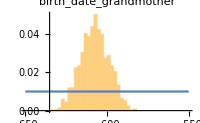
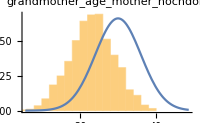
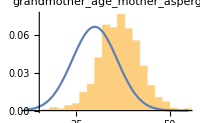
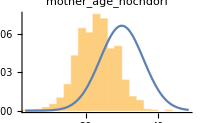
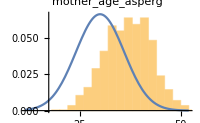
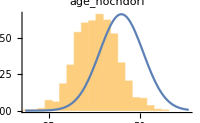
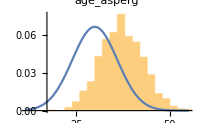
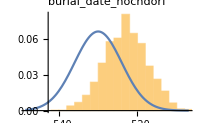

```mathematica
Module[
{d,pd,left,right},
Row[
Table[
v=variableNames[[i]];
d=stanData[All,v];
pd=priorDists[[i]];
left=Min[Quantile[d,0.001],Quantile[pd,0.001]];
right=Max[Quantile[d,0.999],Quantile[pd,0.999]];
Show[
Histogram[d,Automatic,"PDF",PlotLabel->v,ImageSize->200,Axes->{True,False}],
Plot[PDF[pd,x],{x,left,right}],
PlotRangeClipping->True,PlotRange->{{left, right},All}
],
{i,Length@variableNames}
],
Spacer[20]
]
]
```

```mathematica
TableForm[Table[Quantile[stanData[All,v],#]&/@{0.05,0.5,0.95},{v,variableNames}],TableHeadings->{variableNames,{"5-Percentile","Median","95-Percentile"}}]
```

| 5-Percentile | Median | 95-Percentile
birth_date_grandmother | -622.04 | -607.38 | -593.347
grandmother_age_mother_hochdorf | 13.2463 | 23.2283 | 32.7616
grandmother_age_mother_asperg | 27.5552 | 36.476 | 45.7379
mother_age_hochdorf | 14.5799 | 22.9973 | 31.5982
mother_age_asperg | 27.3625 | 37.1645 | 46.0453
age_hochdorf | 29.0454 | 38.1298 | 47.8337
age_asperg | 27.9791 | 36.9924 | 46.3721
burial_date_hochdorf | -532.029 | -523.063 | -513.945
burial_date_asperg | -505.846 | -496.773 | -487.498

```mathematica
paramNames=variableNames[[;;-3]]
```

{birth_date_grandmother,grandmother_age_mother_hochdorf,grandmother_age_mother_asperg,mother_age_hochdorf,mother_age_asperg,age_hochdorf,age_asperg}

```mathematica
combinedPrior=ProductDistribution@@(priorDists[[;;-3]])
```

ProductDistribution[UniformDistribution[{-650,-550}],NormalDistribution[30,6],NormalDistribution[30,6],NormalDistribution[30,6],NormalDistribution[30,6],NormalDistribution[45,6],NormalDistribution[30,6]]

```mathematica
logLcousins[paramVector_]:=Module[{grandMothersBirthDate,birthAgeMotherH,birthAgeMotherA,birthAgeH,birthAgeA,ageH,ageA,burialDateH,burialDateA},
{grandMothersBirthDate,birthAgeMotherH,birthAgeMotherA,birthAgeH,birthAgeA,ageH,ageA}=paramVector;
burialDateH=grandMothersBirthDate+birthAgeMotherH+birthAgeH+ageH;
burialDateA=grandMothersBirthDate+birthAgeMotherA+birthAgeA+ageA;
LogLikelihood[combinedPrior,{paramVector}]+LogLikelihood[NormalDistribution[-530.,6],{burialDateH}]+
LogLikelihood[NormalDistribution[-490.,6],{burialDateA}]
]
```

```mathematica
posteriorDraws=stanData[All,paramNames/*Values]//Normal;
```

```mathematica
posteriorLogLvalues=logLcousins/@posteriorDraws;
```

```mathematica
logMarginalLikelihood[posteriorDraws,posteriorLogLvalues,logLcousins]
```

Estimating α as 9.29185

Estimating piHat as 0.27

-13.5687

## Summary

```mathematica
logMarginalLikelihoods={-15.285171768924048,-9.60377925296963,-13.568659796286394};
params={5,6,7};
```

```mathematica
Sort[{1,3,2}]
```

{1,2,3}

```mathematica
relativeProbabilities=Exp[logMarginalLikelihoods-Max@logMarginalLikelihoods];
relativeProbabilities/=Total@relativeProbabilities;
bayesFactors={"n/a",relativeProbabilities[[2]]/relativeProbabilities[[3]],relativeProbabilities[[3]]/relativeProbabilities[[1]]};
```

```mathematica
TableForm[
Transpose@{params,logMarginalLikelihoods,relativeProbabilities,bayesFactors},
TableHeadings->{{"(Half-)siblings","Avuncular","(Double) First Cousins"}, {"Anzahl Parameter","Log-Evidence","Relative\nprobability","Bayes Factor over\nnext-best model"}}
]
```

| Anzahl Parameter | Log-Evidence | Relative
probability | Bayes Factor over
next-best model
(Half-)siblings | 5 | -15.2852 | 0.00333419 | n/a
Avuncular | 6 | -9.60378 | 0.978111 | 52.714
(Double) First Cousins | 7 | -13.5687 | 0.0185551 | 5.56508